## Funciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2.(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Unitary[θ,α,ϕ,t]
```

SparseArray[…]

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[HadamardMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Estado aleatorio

```mathematica
QubitState[θ_,ϕ_]:={Cos[θ/2] ,Exp[I ϕ] Sin[θ/2] }
```

```mathematica
ClearAll@RandomQubitState
```

```mathematica
RandomQubitState[seed_:Automatic,fixedθ_:Automatic,fixedϕ_:Automatic]:=Module[{θ,ϕ,u1,u2},If[seed=!=Automatic,SeedRandom[seed]];
u1=RandomReal[];u2=RandomReal[];θ=If[fixedθ===Automatic,ArcCos[2 u1-1],fixedθ];
ϕ=If[fixedϕ===Automatic,2 Pi u2,fixedϕ];
{θ,ϕ,Cos[θ/2],Exp[I ϕ] Sin[θ/2]}]
```

```mathematica
RandomQubitState[123]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
RandomQubitState[123,π/2.,Automatic]
```

{1.5708,6.14386,0.707107,0.700255-0.0981984 ⅈ}

```mathematica
RandomQubitState[123,Automatic,Automatic]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
QubitState[1.6594742299456648,6.1438614455765235]
```

{0.67507,0.730605-0.102455 ⅈ}

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

### Extraer datos para FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[varyingAlpha_List,t_Integer]:=Flatten[{#[[1;;2]],#[[4,t+1]]}]&/@varyingAlpha
```

### Extraer datos para SphereGraph

```mathematica
ExtractDataSphereGraph[varyingAlpha_List]:=Flatten[{#[[1;;2]],#[[5]]}]&/@varyingAlpha
```

## Funciones gráficas

### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
],
opts
]
```

```mathematica
PosProbDisTimePlot[P2]
```

PosProbDisTimePlot[P2]

### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

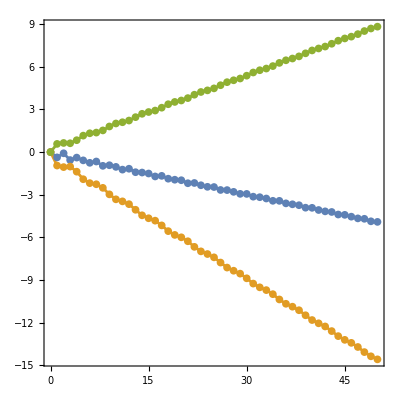

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

G=CalculateData[coin0,θ1,α1,ϕ1,t];
H=CalculateData[coin0,θ2,α2,ϕ2,t];
J=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[{G[[2]],H[[2]],J[[2]]},t,PlotLegends->{"","",""}]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{θ,0,2 Pi,Appearance->"Labeled"},
{α,0,Pi,Appearance->"Labeled"},
{ϕ,0,2 Pi,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer,θi_:0,αi_,ϕi_]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{{θ,θi},0,2 Pi,Appearance->"Labeled"},
{{α,αi},0,Pi,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 Pi,Appearance->"Labeled"}
]
```

### Valor de expectación para un tiempo fijo

```mathematica
ClearAll@FixedTimeExpValPlot
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/nα,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,αLabels_Integer,ϕLabels_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{αLabels*i π/nα,ToString[TraditionalForm[αLabels*i π/nα]]},{i,0,nα}];
phiTicks=Table[{ϕLabels*i*2π/nϕ,ToString[TraditionalForm[ϕLabels*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

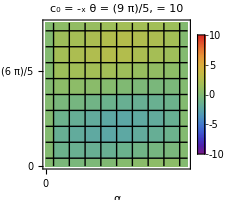

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
fixedt=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataExpVal[res,fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,θ,nα,nϕ]
```

### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[data_List,initCoinState_,θ_,opts:OptionsPattern[Graphics3D]]:=Module[{sphere},
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.03],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

RGBColor["#00D52C"],Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Indefinido"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],",    θ = ",θ}],
opts
]
]
```

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataSphereGraph[res];
SphereGraph[data,coin0,θ]
```

-Graphics3D-

### Valor de expectación contra θ

```mathematica
ClearAll@ExpValVsThetaPlot
```

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->Large]
]
```

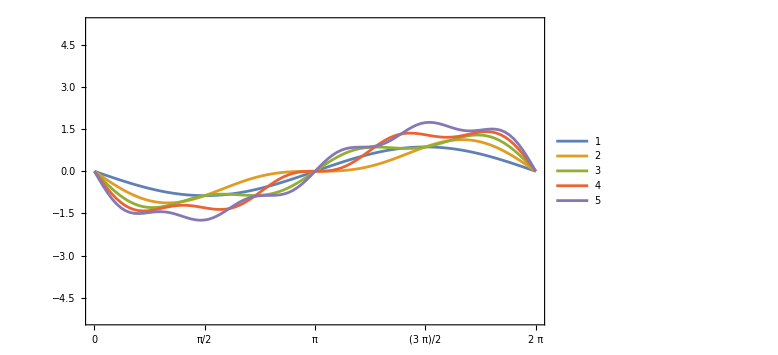

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t=5;

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,times_List]:=Module[{thetaVals,expecVals,maxT},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,times}];
maxT=Max[times];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[times,
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(maxT+0.05 maxT),maxT+0.05 maxT}},
PlotStyle->ColorData[97]/@Range[Length[times]],
ImageSize->Large]
]
```

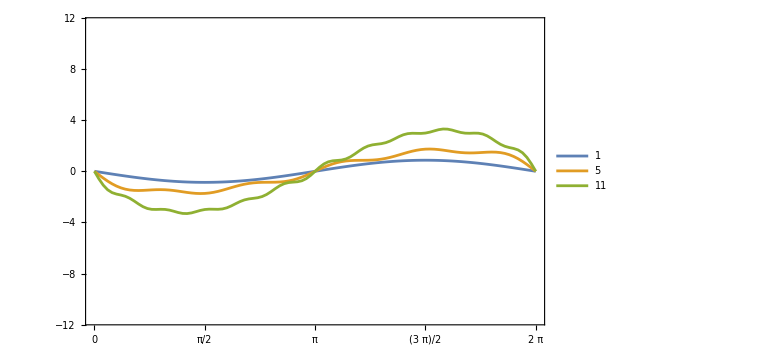

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t={1,5,11};

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ClearAll@ExpValVsThetaManipulate
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5,αi_,ϕi_]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{{α,αi},0,π,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 π,Appearance->"Labeled"}
]
```

```mathematica
coin0=plusX;
t=5;
αi=π/2.;
ϕi=π/3.;
ExpValVsThetaManipulate[coin0,t]
```

```mathematica
ExpValVsThetaManipulate[coin0_,times_List]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,times],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

```mathematica
ExpValVsThetaManipulate[coin0_,times_List,αi_,ϕi_]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,times],
{{α,αi},0,π,Appearance->"Labeled"},
{{ϕ,ϕi},0,2 π,Appearance->"Labeled"}
]
```

```mathematica
coin0=plusX;
t={5,10};
αi=π/2.;
ϕi=π/3.;
ExpValVsThetaManipulate[coin0,t]
```

### Valor de expectación contra θ promediado en el tiempo

```mathematica
AvrgExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}]/t,{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->Large]
]
```

```mathematica
AvrgExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
AvrgExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

### Diagramas de fase

```mathematica
L[θ_,θa_,θb_]:=θa<=Mod[θ,2 Pi]<=θb;
W[θ_,θa_,θb_]:=Mod[θ,2 Pi]<=θa||Mod[θ,2 Pi]>=θb;
```

```mathematica
PhaseDiagramPlot[θa_,θb_,α_,ϕ_,β0_,γ0_]:=Module[{fs,fsf},
fs=17;fsf=20;

RegionPlot[{
L[x1,θa,θb]&&L[x2,θa,θb]&&W[x1+x2,θa,θb],
W[x1,θa,θb]&&W[x2,θa,θb]&&L[x1+x2,θa,θb],
W[x1,θa,θb]&&W[x2,θa,θb]&&W[x1+x2,θa,θb],
L[x1,θa,θb]&&L[x2,θa,θb]&&L[x1+x2,θa,θb],(L[x1,θa,θb]&&W[x2,θa,θb]&&W[x1+x2,θa,θb])||(W[x1,θa,θb]&&L[x2,θa,θb]&&W[x1+x2,θa,θb]),(L[x1,θa,θb]&&W[x2,θa,θb]&&L[x1+x2,θa,θb])||(W[x1,θa,θb]&&L[x2,θa,θb]&&L[x1+x2,θa,θb])
},
{x1,0,2 π},{x2,0,2 π},
PlotRange->{{-0.,2Pi+0.},{-0.,2Pi+0.}},
PlotPoints->50,
FrameLabel->{Style["",FontSize->fsf],Style["",FontSize->fsf]},
FrameTicks->{Table[{k,TraditionalForm[k]},{k,0,2π,π/2}],Table[{k,TraditionalForm[k]},{k,0,2π,π/2}]},
FrameStyle->Directive[Black,FontSize->fs],
GridLines->Automatic,
ImageSize->550,
PlotLabel->Style[Row[{" ", NumberForm[α/π,{Infinity,3}],
 " ",NumberForm[ϕ/π,{Infinity,3}], ",","    ",NumberForm[β0/π,{Infinity,3}]," ",
NumberForm[γ0/π,{Infinity,3}],""}],
FontSize->fs
],
PlotLegends->SwatchLegend[Automatic,{"LL=W","WW=L","WW=W","LL=L","LW=W","LW=L"},
LegendMarkerSize->20
]
]
]
```

## Verificación

```mathematica
{a,b}=RandomQubitState[706,π/2.,Automatic][[3;;]]
```

{0.707107,0.693097+0.140061 ⅈ}

```mathematica
{β,γ}=RandomQubitState[706,π/2.,Automatic][[;;2]]
```

{1.5708,0.199394}

## Prueba 1

```mathematica
{α,ϕ}=RandomQubitState[607,Automatic,Automatic][[;;2]]
```

{1.70462,6.05675}

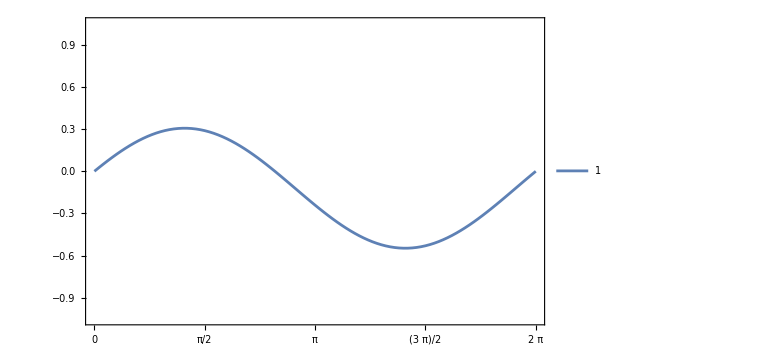

```mathematica
coin0={a,b};
t=1;

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.409379

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.379577

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

2.56941

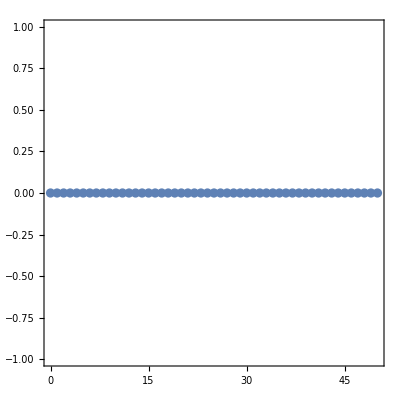

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.14159

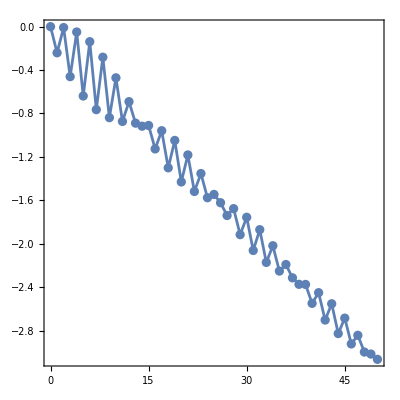

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.409379

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.620423

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

0.572183

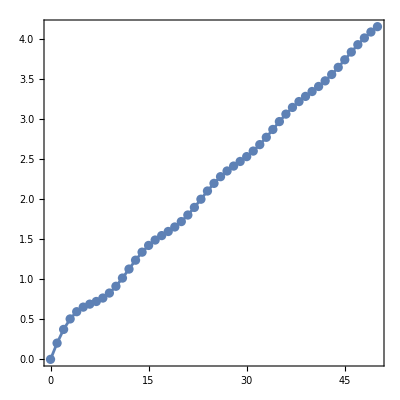

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Cálculos viejos

### Ecuación 12

```mathematica
A3=Norm[a]^2
```

0.5

```mathematica
B3= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

-0.409379

```mathematica
C3=Norm[a Cos[α]+Exp[-ⅈ ϕ]b Sin[α]]^2
```

0.379577

```mathematica
θ3Plus=ArcCos[-(A3+C3-1)/Sqrt[(A3-C3)^2+(B3)^2]]+ArcTan[B3/(A3-C3)]
```

4.44089×10^-16

```mathematica
coin0={a,b};
θ=θ3Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ3Minus=ArcCos[-(A3+C3-1)/(-Sqrt[(A3-C3)^2+(B3)^2])]+ArcTan[B3/(A3-C3)]
```

0.572183

```mathematica
coin0={a,b};
θ=θ3Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A4=Norm[b]^2
```

0.5

```mathematica
B4= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

-0.409379

```mathematica
C4=Norm[b Cos[α]-Exp[ⅈ ϕ]a Sin[α]]^2
```

0.620423

```mathematica
θ4Plus=ArcCos[-(A4+C4-1)/Sqrt[(A4-C4)^2+(B4)^2]]+ArcTan[B4/(A4-C4)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ4Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ4Minus=ArcCos[-(A4+C4-1)/(-Sqrt[(A4-C4)^2+(B4)^2])]+ArcTan[B4/(A4-C4)]
```

2.56941

```mathematica
coin0={a,b};
θ=θ4Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 2

```mathematica
{α,ϕ}=RandomQubitState[67,Automatic,Automatic][[;;2]]
```

{2.73212,1.83464}

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

-0.397297

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.523522

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

3.14159

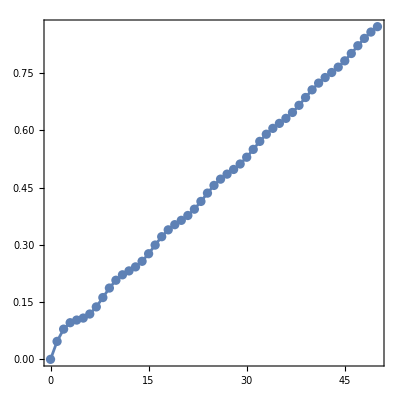

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.02332

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

-0.397297

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.476478

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

-6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

0.118273

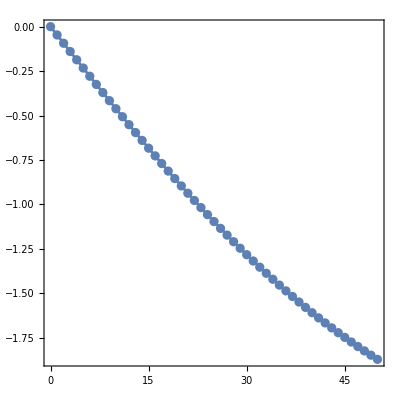

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

## Cálculos viejos

### Ecuación 12

```mathematica
A3=Norm[a]^2
```

0.5

```mathematica
B3= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

0.397297

```mathematica
C3=Norm[a Cos[α]+Exp[-ⅈ ϕ]b Sin[α]]^2
```

0.523522

```mathematica
θ3Plus=ArcCos[-(A3+C3-1)/Sqrt[(A3-C3)^2+(B3)^2]]+ArcTan[B3/(A3-C3)]
```

0.118273

```mathematica
coin0={a,b};
θ=θ3Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ3Minus=ArcCos[-(A3+C3-1)/(-Sqrt[(A3-C3)^2+(B3)^2])]+ArcTan[B3/(A3-C3)]
```

-4.44089×10^-16

```mathematica
coin0={a,b};
θ=θ3Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A4=Norm[b]^2
```

0.5

```mathematica
B4= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

0.397297

```mathematica
C4=Norm[b Cos[α]-Exp[ⅈ ϕ]a Sin[α]]^2
```

0.476478

```mathematica
θ4Plus=ArcCos[-(A4+C4-1)/Sqrt[(A4-C4)^2+(B4)^2]]+ArcTan[B4/(A4-C4)]
```

3.02332

```mathematica
coin0={a,b};
θ=θ4Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ4Minus=ArcCos[-(A4+C4-1)/(-Sqrt[(A4-C4)^2+(B4)^2])]+ArcTan[B4/(A4-C4)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ4Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 3

```mathematica
{a,b}=RandomQubitState[706,π/2.,3π/4.][[3;;]]
```

{0.707107,-0.5+0.5 ⅈ}

```mathematica
{β,γ}=RandomQubitState[706,π/2.,3π/4.][[;;2]]
```

{1.5708,2.35619}

```mathematica
{α,ϕ}={π/4.,π/4.}
```

{0.785398,0.785398}

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.707107

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.5

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.707107

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.5

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

0.

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

0.

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 4

```mathematica
{a,b}=RandomQubitState[706,π/2.,Automatic][[3;;]]
```

{0.707107,0.693097+0.140061 ⅈ}

```mathematica
{β,γ}=RandomQubitState[706,π/2.,Automatic][[;;2]]
```

{1.5708,0.199394}

```mathematica
{α,ϕ}={3π/4.,5π/4.}
```

{2.35619,3.92699}

## Cálculos nuevos

### P(1)=1/2

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.391056

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.916579

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

1.63398

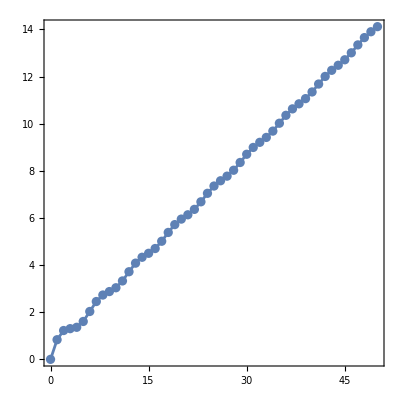

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

-6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### P(-1)=1/2

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.391056

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.0834213

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

1.50761

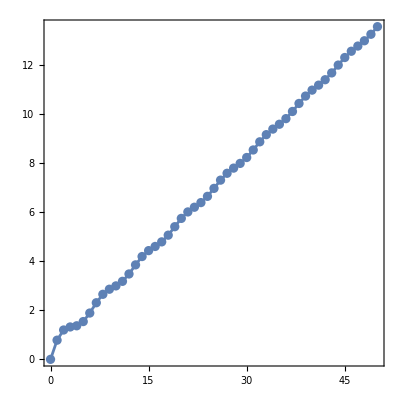

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

3.14159

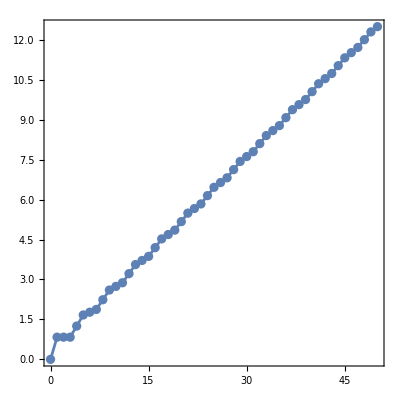

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```